```mathematica
(* materials: https://github.com/JarekDuda/SGD-OGR-Hessian-estimator/ *)
```

```mathematica
(* basic step using g: noisy gradient in θ *)
step[ng_]:=(m+=γ(ng-m);                                  (* update momentum, averages: *)
mθ+=β(θ-mθ);mθθ+=β(KroneckerProduct[θ-mθ,θ-mθ]-mθθ);
mg+=β(ng-mg);mgθ+=β(KroneckerProduct[ng-mg,θ-mθ]-mgθ);
mgθs=mgθ+Transpose[mgθ];{e,ev}=Eigensystem[mθθ];
pH=Transpose[ev].((ev.mgθs.Transpose[ev])/
(Table[e,d]+Transpose[Table[e,d]])).ev;      (* Hessian estimator *) 
θ-=ma[pH].m);                        (* 1/|~eigenvalues of pH: predicted Hessian| *)
eh[lm_]:=1/Map[Max[#,cut]&,Abs[lm]*div];   (* eigenvalue inv, div&cut *)
ma[A_]:=({e,ev}=Eigensystem[A];Transpose[ev].DiagonalMatrix[eh[e]].ev);

    (* Beale function, initialization, hyperparameters: *)
f=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x*y^3)^2;
v={x,y};d=Length[v];sub[p_]:=Table[v[[i]]->p[[i]],{i,d}];
g=Grad[f,v];H=Table[D[f,v1,v2],{v1,v},{v2,v}];
noise:=RandomReal[NormalDistribution[0,ϵ],d];ϵ=0.1;
β=0.5;γ=0.9;div=1.5;cut=10;    (* hyperparameters *)
m=mg=mθ=Table[0.,d]; θ={0,0}; (*starting position *)
mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];st=30;
Do[step[(g/.sub[θ])+noise],{i,st}]; (* optimization *)
f/.sub[θ]
```

0.0048617

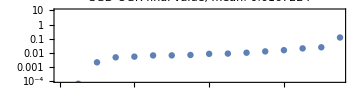

```mathematica
(* hyperparameter optimization, ideally modified during  *)
fv={};β=0.5;γ=0.9;div=1.5;cut=10; steps=30;
paths=Table[m=mg=mθ=Table[0.,d];θh={}; θ={sx,sy};  (*starting position *)
mgθ=Table[0.,d,d];mθθ=IdentityMatrix[d];
Do[AppendTo[θh,θ];step[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-1,1},{sy,-2,2}];
plo=ListLogPlot[Sort[fv],PlotRange->{0.0001,10},PlotTheme->"Detailed",ImageSize->Medium,AspectRatio->1/4,PlotLabel->Row[{"SGD-OGR final value, mean: ",Mean[fv]}]]
```

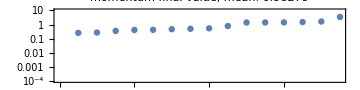

```mathematica
(* comparison with momentum method  *)
fv={};γ=0.5;α=0.017; steps=30;
stepmom[ng_]:=(m+=γ(ng-m);θ-=α*m);                 (* momentum , for α=0.018  one escapes to infinity *)
paths=Table[m=Table[0.,d];θh={}; θ={sx,sy}; (*starting position *)
Do[AppendTo[θh,θ];stepmom[(g/.sub[θ])+noise],{i,steps}]; (* optimization *)
AppendTo[fv,f/.sub[θ]];path=Table[Append[θ,f/.sub[θ]],{θ,θh}],{sx,-1,1},{sy,-2,2}];
plm=ListLogPlot[Sort[fv],PlotRange->{0.0001,10},PlotTheme->"Detailed",AspectRatio->1/4,ImageSize->Medium,PlotLabel->Row[{"momentum final value, mean: ",Mean[fv]}]]
```

```mathematica
(* draw the paths *)
```

```mathematica
Row[{Grid[Table[path=paths[[i,j]];mnmx=Map[MinMax,Transpose[path]];
Show[Plot3D[f,{x,mnmx[[1,1]],mnmx[[1,2]]},{y,mnmx[[2,1]],mnmx[[2,2]]},ImageSize->Small],Graphics3D[{Thickness[0.03],Line[path,VertexColors->Map[Hue,Range[steps]/steps/2]]}]]
,{i,Length[paths]},{j,Length[paths[[1]]]}],Spacings->{-0.2,-2}],
Column[{"step",Grid[Transpose[{Range[steps],Map[Hue,Range[steps]/steps/2]}],Spacings->{0,-0.1}]}]}]
```